```mathematica
(*Exit[];*)
```

```mathematica
NotebookDelete/@Select[Cells[GeneratedCell->False],StringMatchQ[First@FrontEndExecute[FrontEnd`ExportPacket[NotebookRead@#,"InputText"]],(" "|"\t"|"\r"|"\n"|"
")...]&];
ClearMemory:=Module[{},Unprotect[In,Out];
Clear[In,Out];
Protect[In,Out];
ClearSystemCache[];];
```

```mathematica
temp=Import[NotebookDirectory[]<>"../output/yield-240701-omp-t.dat","Table"];
```

```mathematica
labels = First[temp][[2;;6]]
points=Rest[temp];
structuredData={#[[1;;3]],#[[5]]}&/@points;
Print[Take[structuredData,5]](*Print the first 5 structured data points*)

localYield=Interpolation[structuredData]
```

{pT,phi_p,y_p,dNd3p,dNd3p}

{{{0.,0.,-1.},132.012078753789723},{{0.,0.20944,-1.},132.012078753789723},{{0.,0.418879,-1.},132.012078753789723},{{0.,0.628319,-1.},132.012078753789723},{{0.,0.837758,-1.},132.012078753789723}}

InterpolatingFunction[…]

```mathematica
structuredData[[1]]
```

{{0.,0.,-1.},132.012078753789723}

```mathematica
localYield[0,0,-1]
```

132.012

```mathematica
dNd3p[pT_,phi_,y_]:=localYield[pT,phi,y]
```

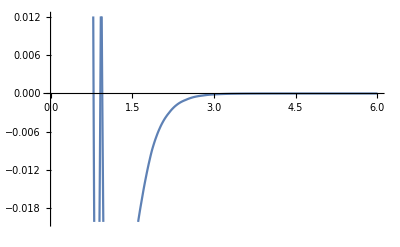

```mathematica
Plot[dNd3p[pT,0,0],{pT,0,6}]
```

```mathematica
vol=NIntegrate[dNd3p[pT,phi,y]pT,{phi,0,2Pi},{pT,0,6.2},{y,-1,1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 43.6999 and 0.0000619778 for the integral and error estimates.

```mathematica
dNdy[y_]:=NIntegrate[dNd3p[pT,phi,y]pT,{phi,0,2Pi},{pT,0,6.2}]
```

```mathematica
dNdP[pT_]:=NIntegrate[dNd3p[pT,phi,y]pT,{phi,0,2Pi},{y,-1,1}]
```

```mathematica
vol
```

43.6999

```mathematica
dNdy[0.001]
```

9.85402

```mathematica
dNdP[0]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
yield1=Table[{pT,dNdP[pT]/vol},{pT,0,6.2,0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
yield2=Table[{y,dNdy[y]/vol},{y,-1,1,0.01}];
```

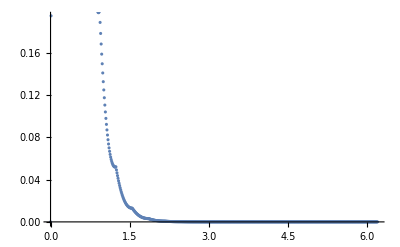

```mathematica
ListPlot[yield1,PlotRange->Automatic]
```

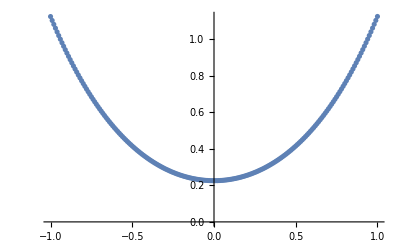

```mathematica
ListPlot[yield2]
```

```mathematica
v1[pT_]:=1/vol NIntegrate[dNd3p[pT,phi,y]*Sin[phi],{phi,0,2Pi},{y,-1,1}]
```

```mathematica
v2[pT_]:=1/vol NIntegrate[dNd3p[pT,phi,y]*Cos[phi],{phi,0,2Pi},{y,-1,1}]
```

```mathematica
v1list=Table[{pT,v1[pT]},{pT,0.01,6.2,0.1}];
```

```mathematica
v2list=Table[{pT,v2[pT]},{pT,0,6.2,0.1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

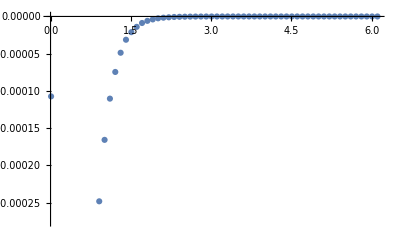

```mathematica
ListPlot[v1list]
```

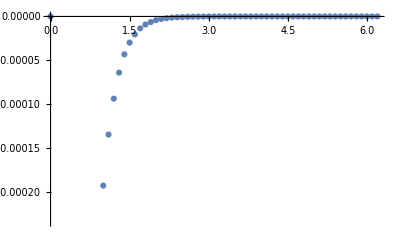

```mathematica
ListPlot[v2list]
```